```mathematica
4593/3600.
```

1.27583

```mathematica
Clear[th,fpos,fneg,gpara]
```

```mathematica
myconsts={l->-nu,nu->3,r->20,nn->2.,newthpower->4}
```

{l→-nu,nu→3,r→20,2→2.,newthpower→4}

```mathematica
rshift=4
rpower=3/4
thpower=4
nn=2
myr=(r+rshift)^rpower
myz=myr*Cos[th]
myR=myr*Sin[th]
myvert=If[th>Pi/2,myr*Sin[th],myr*Sin[-th]]
```

4

3/4

4

2

(4+r)^(3/4)

(4+r)^(3/4) Cos[th]

(4+r)^(3/4) Sin[th]

If[th>π/2,myr Sin[th],myr Sin[-th]]

```mathematica
fneg[th_]:=1-Cos[th]^thpower
fpos[th_]:=1+Cos[th]^thpower
factor=2 (1-Log[2])
(*factor=0*)
gpara[th_]:=(1/2)*(myr*fneg[th]+2*fpos[th]*(1-Log[fpos[th]]))-factor
```

2 (1-Log[2])

```mathematica
gpara[0]
```

0

π-th

If[th<π/2,-2 (1-Log[2])+1/2 ((4+r)^(3/4) (1-Cos[th]^4)+2 (1+Cos[th]^4) (1-Log[1+Cos[th]^4])),-2 (1-Log[2])+1/2 ((4+r)^(3/4) (1-Cos[th]^4)+2 (1+Cos[th]^4) (1-Log[1+Cos[th]^4]))]

Cos[th] If[th<π/2,-2 (1-Log[2])+1/2 ((4+r)^(3/4) (1-Cos[th]^4)+2 (1+Cos[th]^4) (1-Log[1+Cos[th]^4])),-2 (1-Log[2])+1/2 ((4+r)^(3/4) (1-Cos[th]^4)+2 (1+Cos[th]^4) (1-Log[1+Cos[th]^4]))]

((4+r)^(3/4)+2 Log[2]) th^2+O[th]^4

Cos[th] If[th<π/2,-2 (1-Log[2.])+1/2 ((4+20)^(3/4) (1-Cos[th]^4)+2. (1+Cos[th]^4) (1-Log[1+Cos[th]^4])),-2 (1-Log[2.])+1/2 ((4+20)^(3/4) (1-Cos[th]^4)+2. (1+Cos[th]^4) (1-Log[1+Cos[th]^4]))]

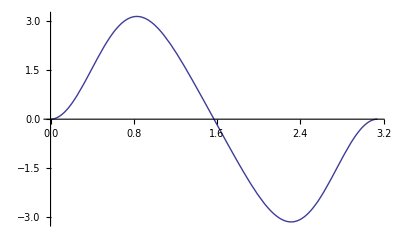

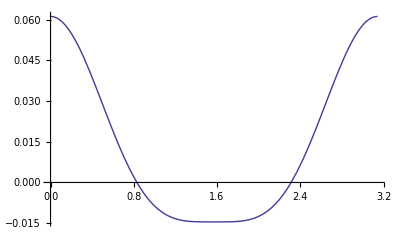

```mathematica
thother=Pi-th
gparalow=Evaluate[gpara[th]];
gparahigh=Evaluate[gpara[thother]];
mygpara=If[th<Pi/2,Evaluate[gparalow],Evaluate[gparahigh]]
aphi=mygpara*Cos[th]^(1)*Sin[th]^(0)

Series[aphi,{th,0,3}]
plotaphi=Evaluate[aphi]//.myconsts
Plot[plotaphi,{th,0,Pi}]

B1=D[plotaphi,th]/(r^2*Sin[th])//.myconsts;
B1//.{th->Pi/4};
Plot[B1,{th,0,Pi}]
```

```mathematica
(* require A_\phi \propto \theta^2 + O(\theta^4) *)
```

If[th<π/2,1-Cos[th]^newthpower,1-Cos[π-th]^newthpower]

Cos[th]-Cos[th]^5

2 th^2+O[th]^4

Cos[th]-Cos[th]^5

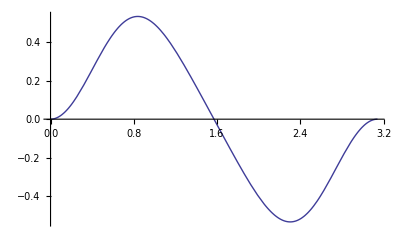

1/400 Csc[th] (-Sin[th]+5 Cos[th]^4 Sin[th])

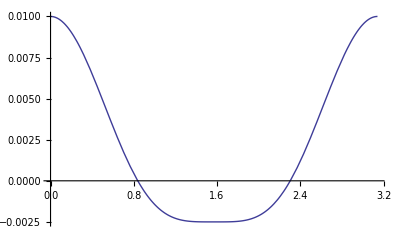

```mathematica
switch=If[th<Pi/2,1-Cos[th]^newthpower,1-Cos[Pi-th]^newthpower]
aphi=FullSimplify[Cos[th]^1*switch//.myconsts,{th>0}]
Series[aphi,{th,0,3}]
plotaphi=Evaluate[aphi]//.myconsts
Plot[plotaphi,{th,0,Pi}]

B1=D[plotaphi,th]/(r^2*Sin[th])//.myconsts
Plot[B1,{th,0,Pi}]
```

{l→-nu,nu→3,r→3,2→2.}

-3 Cos[th] √(1-Cos[th]^2.) Sin[th]

-3. th^2+O[th]^4

-3 Cos[th] √(1-Cos[th]^2.) Sin[th]

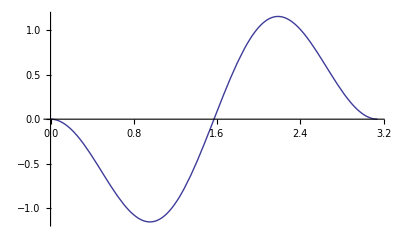

1/9 Csc[th] (-3 Cos[th]^2. √(1-Cos[th]^2.)-(3. Cos[th]^2. Sin[th]^2.)/(√(1-Cos[th]^2.))+3 √(1-Cos[th]^2.) Sin[th]^2.)

-0.166667

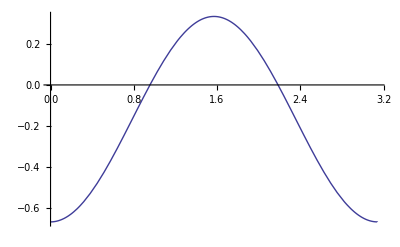

```mathematica
myconsts={l->-nu,nu->3,r->3,nn->2.}
aphi=FullSimplify[Sin[th]*LegendreP[l,1,Cos[th]]//.myconsts,{th>0}]
Series[aphi,{th,0,3}]
plotaphi=Evaluate[aphi]//.myconsts
Plot[plotaphi,{th,0,Pi}]

B1=D[plotaphi,th]/(r^2*Sin[th])//.myconsts
B1//.{th->Pi/4}
Plot[B1,{th,0,Pi}]
```

```mathematica
LegendreP[4,Cos[x]]
```

1/8 (3-30 Cos[x]^2+35 Cos[x]^4)

```mathematica
LegendreQ[0,1,Cos[2.]]
```

-1.09975

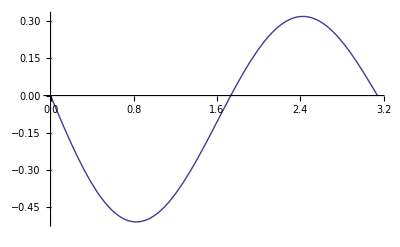

```mathematica
Plot[Sin[th]^2*LegendreQ[-3/4,1,Cos[th]],{th,0,Pi}]
```

```mathematica
Theta=D0*Abs[Sin[th]]*LegendreP[l,1,Cos[th]]+D1*Abs[Sin[th]]*LegendreQ[l,1,Cos[th]]//.{D1->0}
R=r^nu
Aphi=Theta*R
```

D0 Abs[Sin[th]] LegendreP[l,1,Cos[th]]

r^nu

D0 r^nu Abs[Sin[th]] LegendreP[l,1,Cos[th]]

```mathematica
Aphi1=Aphi//.{l->-nu,nu->3/4,D0->1}
Aphi2=Aphi//.{l->(nu-1),nu->3/4,D0->1}
```

r^(3/4) Abs[Sin[th]] LegendreP[-3/4,1,Cos[th]]

r^(3/4) Abs[Sin[th]] LegendreP[-1/4,1,Cos[th]]

```mathematica
Aphi1plot=Aphi1//.{r->3}
Aphi2plot=Aphi2//.{r->3}
```

3^(3/4) Abs[Sin[th]] LegendreP[-3/4,1,Cos[th]]

3^(3/4) Abs[Sin[th]] LegendreP[-1/4,1,Cos[th]]

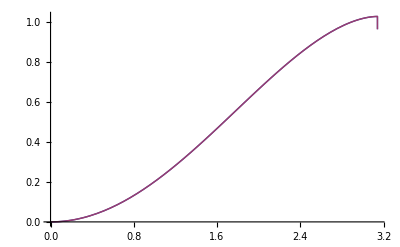

```mathematica
Plot[{Aphi1plot,Aphi2plot},{th,0,Pi}]
```